## Annihilations

```mathematica
Clear["Global`*"];
ClearSystemCache[];
SetDirectory[NotebookDirectory[]];
```

```mathematica
tempConversion = (1*^-9/(1.16*^4)); (* GeV *)
NM     = (0.939); (* GeV *)
SOL   = 299792458.; (* ms^-1 *)
VELDISP  = 270.*^3;(* ms^-1 *)
NSVEL =  200.*^3 ;(* ms^-1 *)
G       =  6.67408*^-11; (*Grav Constant*)
TT = ((1*^10 * 3.154*^7)/(6.58*^-16)*1*^9); (* therm time *)
hBar = 1.054571800*^-34;


vAvg[mx_, temp_] := (6*temp*tempConversion)/mx;

capRate = 1.*^22*6.58*^-16*1*^-9; (*test cap rate*)
```

## NS Data

```mathematica
EoSHeaders = Import["eos_24_lowmass.dat"];
Dataset[EoSHeaders[[1,All]]] (*Print out headings so I know what I'm doing *)
EoSData =Drop[EoSHeaders, 1] ;(* Remove Headings *)
```

Dataset[<>]

```mathematica
radius = EoSData[[All,1]];

rMin = radius[[1]];
rMax = 12.1;

muFn     = Interpolation[ EoSData[[All, {1,8}]] ]; (* Chemical potential in MeV *)
muFe     = Interpolation[ EoSData[[All, {1,10}]] ]; (* Chemical potential in MeV *)
muFμ     = Interpolation[ EoSData[[All, {1,11}]] ]; (* Chemical potential in MeV *)

nb          = EoSData[[All,3]];
Yn          = EoSData[[All, 7]];

NSMass=   Interpolation[EoSData[[All, {1, 2}]]]; (* In units of M_⊙ *)
```

## Number density

```mathematica
rTh[T_, mx_]:=3.265*√(T/10^5)*√(1/mx);
```

```mathematica
ϕ[r_]:= (2*π*G*(7.76*1*^17)*r^2)/3;
```

```mathematica
ndAnFac[mx_, T_, ACS_]:=NIntegrate[x^2*Exp[(-2*mx*ϕ[x])/T]*ACS[x, mx, T],{x, 0, rTh[T, mx]}]/(4*π*(NIntegrate[x^2*Exp[(-2*mx*ϕ[x])/T],{x, 0, rTh[T, mx]}])^2);
```

## Masses

```mathematica
lepMasses = {0.5109989461, 105.6583745, 1776.86, 0,0,0}*1.*^-3;(* {e, μ, τ,Subscript[ν, e], Subscript[ν, μ], Subscript[ν, τ]}*)
quarkMasses = {2.2*^-3, 4.7*^-3, 95*^-3, 1.257, 4.18, 173};(* {u, d, s, c, b, t}  *)
```

```mathematica
fT = {Mean[{0.019, 0.022, 0.012, 0.011, 0.014, 0.018}], Mean[{0.041, 0.049, 0.033, 0.027, 0.036, 0.042}], Mean[{0.14, 0.36, 0.053, 0.045, 0.118, 0.26}]}

fTG = 1. - Sum[fT[[n]], {n, 1, 3}];

DeltaN = {Mean[{-0.4, -0.43, -0.44, -0.43, -0.48, -0.43}],Mean[{0.77, 0.86, 0.84, 0.84, 0.78, 0.84}], Mean[{-0.12, -0.09, -0.03, -0.085, -0.15, -0.08}]}

deltaN = { 0.23,-0.84, 0.05}(* {u, d, s} *)
```

{0.016,0.038,0.162667}

{-0.435,0.821667,-0.0925}

{0.23,-0.84,0.05}

```mathematica
c12 = Sum[(NM*fT[[n]])/quarkMasses[[n]],{n, 1,3}] +(2.*fTG)/27.*(Sum[NM/quarkMasses[[n]], {n, 3, 6}] - NM);
mBar = 1./Sum[1./quarkMasses[[n]], {n, 1, 3}];
C34 = Sum[mBar/quarkMasses[[n]],{n,1,6}];
c34 = Sum[NM/quarkMasses[[n]]*(1 - C34 +mBar)*DeltaN[[n]],{n, 1,3}];
c56 = 3.;
c78 = Sum[DeltaN[[n]], {n, 1, 3}];
c910 = Sum[deltaN[[n]], {n, 1, 3}];
```

## FD approx’s

```mathematica
fde[r_, mx_]:=HeavisideTheta[-muFe[r]*1*^-3 +mx];
fdμ[r_, mx_]:=HeavisideTheta[-muFμ[r]*1*^-3 +mx];
fdoth[r_, mx_] := 1.;
fdSelect[mf_]:= Which[mf == lepMasses[[1]], fde, mf == lepMasses[[2]], fdμ, True, fdoth];
```

## Ann Cross sections

```mathematica
ssACS[r_, mx_, temp_] :=(Sum[(mx^2/(16.*π))*(1. - mf^2/mx^2)^(3/2)*vAvg[mx, temp]*fdSelect[mf][r, mx], {mf, Select[lepMasses, #≤ mx&]}]+Sum[((3.*mx^2)/(16.*π))*(1. - mf^2/mx^2)^(3/2)*vAvg[mx, temp], {mf, Select[quarkMasses, #≤ mx&]}] );
(*================================================================================================================================================================*)

ppACS[r_,mx_, temp_] :=(Sum[(1./(4.*π))*mx^2*Sqrt[1. - mf^2/mx^2]*fdSelect[mf][r, mx](**(1. + ((2.*mx^2- mf)/(8.*(mx^2 - mf^2)))*vAvg[mx, temp])*),{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(4.*π))*mx^2*Sqrt[1. - mf^2/mx^2](**(1. +( (2.*mx^2- mf)/(8.*(mx^2 - mf^2)))*vAvg[mx, temp])*),{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)

vvACS[r_,mx_, temp_] := (Sum[(1./(4.*π))*mx^2*Sqrt[1. - mf^2/mx^2]*fdSelect[mf][r, mx]*((2. +mf^2/mx^2) + (1./12.)*(1. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(4.*π))*mx^2 Sqrt[1. - mf^2/mx^2]*((2. +mf^2/mx^2) + (1./12.)*(1. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)


aaACS[r_,mx_, temp_] := (Sum[(1./(4.*π))*mx^2*Sqrt[1. - mf^2/mx^2]*fdSelect[mf][r, mx]*(mf^2/mx^2 + (1./12.)*(2. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(4.*π))*mx^2*Sqrt[1. - mf^2/mx^2]*(mf^2/mx^2 + (1./12.)*(2. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)

ttACS[r_,mx_, temp_] := (Sum[(1./(4.*π))*mx^2*Sqrt[1. - mf^2/mx^2]*fdSelect[mf][r, mx]*((7.+mf^2/mx^2) + (2./3.)*(1. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(4.*π))*mx^2*Sqrt[1. - mf^2/mx^2]*((7.+mf^2/mx^2) + (2./3.)*(1. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);
```

## Ann rates

```mathematica
anG[ACS_, mx_?NumericQ, temp_?NumericQ] :=1./((0.5*TT)^2*capRate*ndAnFac[mx, temp, ACS]);
```

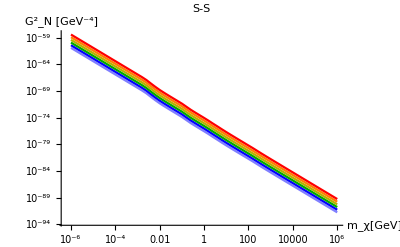

```mathematica
ssPlot = ListLogLogPlot[
 Evaluate@Table[
With[{x:=10^xp},
Table[{x,anG[ssACS, x, T]*c12^2},{xp, -6, 6, 0.2}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}
],

Joined->True, PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red},
AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"}, 
PlotLabel->"S-S", 
LabelStyle->Directive[Black,Bold]]
```

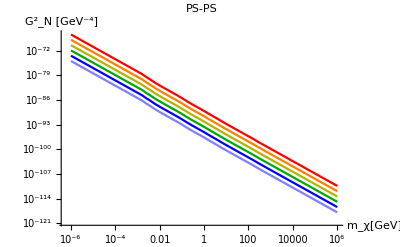

```mathematica
ppPlot =ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,anG[ppACS, x, T]*c34^2},{xp, -6, 6, 0.2}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}], Joined->True,AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"},PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}, PlotLabel->"PS-PS", LabelStyle->Directive[Black,Bold]]
```

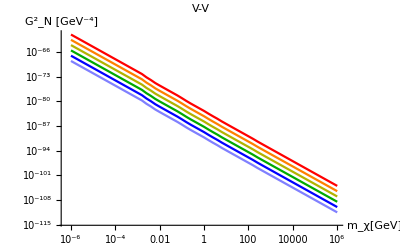

```mathematica
vvPlot =ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,anG[vvACS, x, T]*c56^2},{xp, -6, 6, 0.2}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}], Joined->True,AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"},PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}, PlotLabel->"V-V", LabelStyle->Directive[Black,Bold]]
```

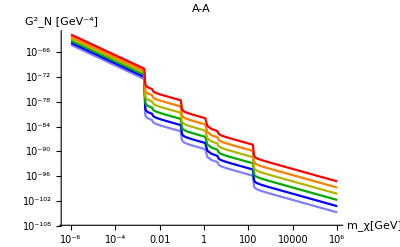

```mathematica
aaPlot =ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,anG[aaACS, x, T]*c78^2},{xp, -6, 6, 0.05}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}], Joined->True,AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"},PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}, PlotLabel->"A-A", LabelStyle->Directive[Black,Bold]]
```

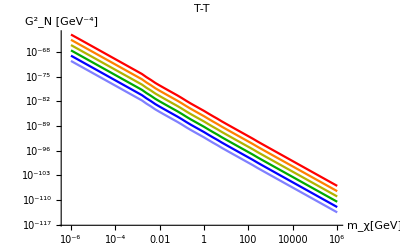

```mathematica
ttPlot =ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,anG[ttACS, x, T]*c910^2},{xp, -6, 6, 0.2}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}], Joined->True,AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"},PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}, PlotLabel->"T-T", LabelStyle->Directive[Black,Bold]]
```

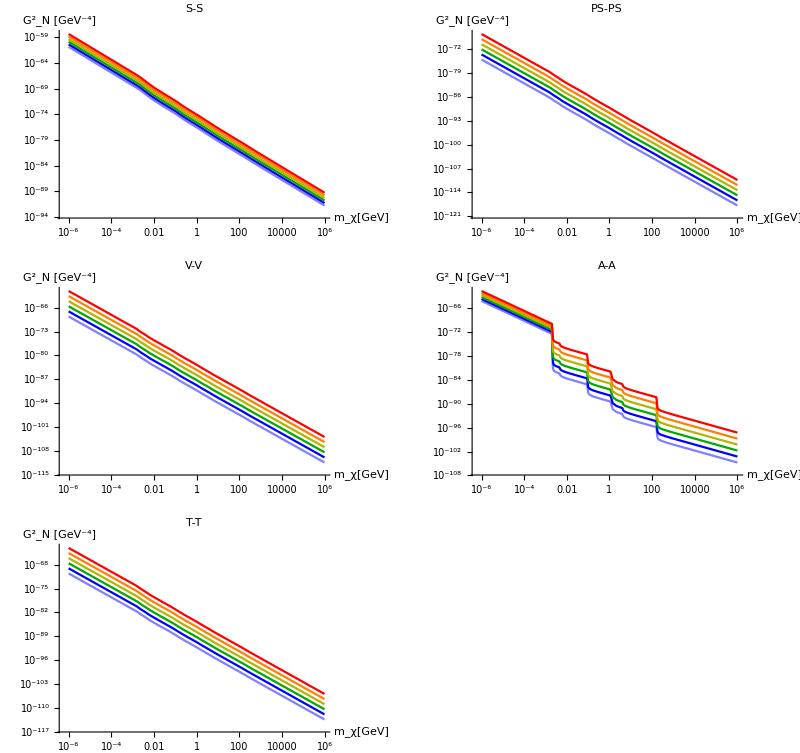

```mathematica
groupedPlots =Legended[GraphicsGrid[{{ssPlot, ppPlot}, {vvPlot, aaPlot}, {ttPlot}}, ImageSize->Full ], LineLegend[Reverse[{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}],Reverse[{"10^1K","10^2K","10^3K","10^4K", "10^5K", "10^6K"}]]]
```

```mathematica
(*Export["ann-limits.pdf", %]*)
```